# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15]}
```

{Frame→True,Axes→False,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],ImageSize→700,FrameTicksStyle→Directive[GrayLevel[0],15]}

## Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Messung Franck-Hertz-Kurve für Quecksilber 2.txt"];
```

```mathematica
data=Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

```mathematica
dataProcessed=data[[All,{2,3}]];
```

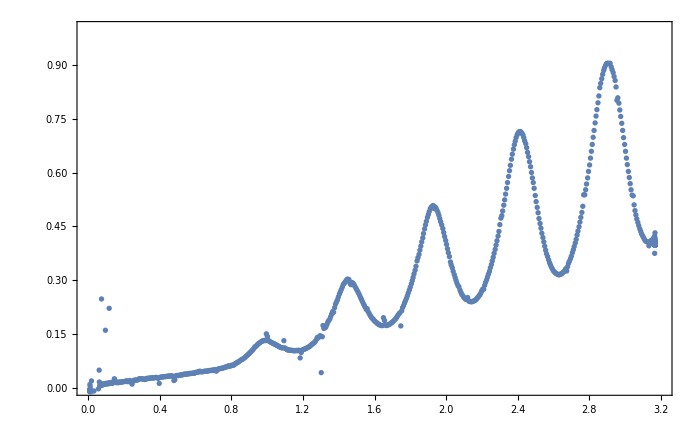

```mathematica
ListPlot[dataProcessed,PlotRange->{{0,3.2},{0,1}},pltsettings]
```

```mathematica
cleanedData=DeleteCases[dataProcessed,x_/;x[[1]]==0.995||x[[1]]==1.001];
```

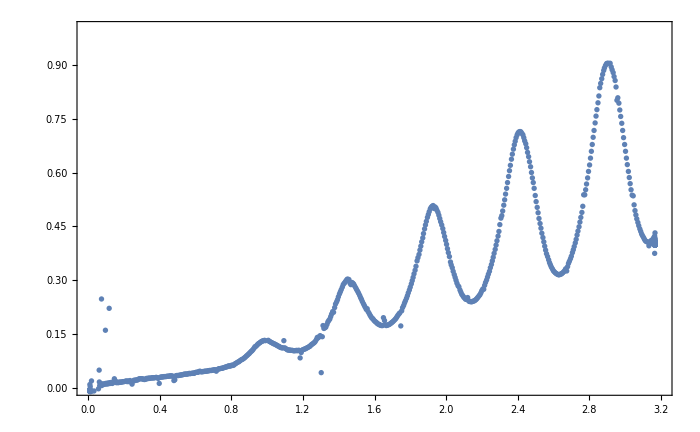

```mathematica
ListPlot[cleanedData,PlotRange->{{0,3.2},{0,1}},pltsettings]
```

```mathematica
intervals={{0.94,1.01},{1.42,1.5},{1.89,1.98},{2.38,2.46},{2.87,2.94}};
```

```mathematica
MaximalBy[{{1,2},{3,4}},Last]
```

{{3,4}}

```mathematica
findPosition[int_]:=MaximalBy[DeleteCases[cleanedData,x_/;x[[1]]<=int[[1]]||x[[1]]>int[[2]]],Last][[1,1]]
```

```mathematica
maxPositions=findPosition/@intervals
```

{0.985,1.447,1.928,2.414,2.902}

```mathematica
colors={Red,Red,Red,Red,Red};
```

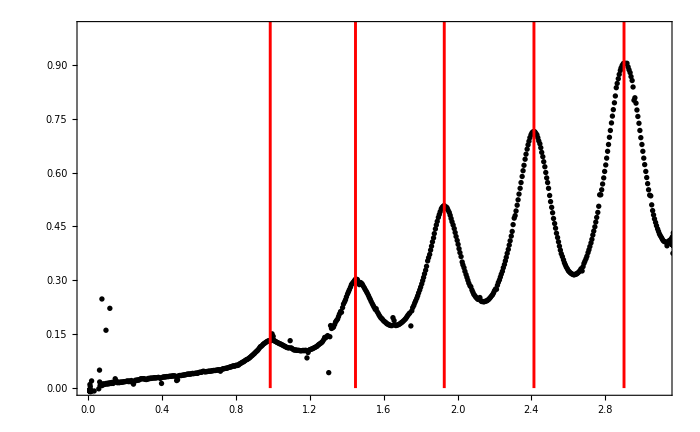

```mathematica
Show[ListPlot[dataProcessed,PlotRange->{{0,3.1},{0,1}},PlotStyle->Black,pltsettings],Graphics[Join@@Table[{Thickness[0.003],colors[[i]],Line[{{maxPositions[[i]],0},{maxPositions[[i]],10}}]},{i,1,Length[maxPositions]}]]]
```

```mathematica
Export[NotebookDirectory[]<>"fig10.pdf",Show[ListPlot[dataProcessed,PlotRange->{{0,3.1},{0,1}},PlotStyle->Black,pltsettings],Graphics[Join@@Table[{Thickness[0.003],colors[[i]],Line[{{maxPositions[[i]],0},{maxPositions[[i]],10}}]},{i,1,Length[maxPositions]}]]],Background->None];
```